```mathematica
dados = Import["/home/mariana/Documentos/Ano_2/FC/Lab/Git_Projetos/P2/Para enviar/2a/RK_generico_2a.txt", "Table"]
```

{{0.01,0.99985,0,0,-0.0299985,0,0},{0.02,0.9994,0,0,-0.059988,0,0},{0.03,0.99865,0,0,-0.0899595,0,0},{0.04,0.997601,0,0,-0.119904,0,0},9992,{99.97,-0.933937,0,0,0.619101,0,0},{99.98,-0.927606,0,0,0.647025,0,0},{99.99,-0.920997,0,0,0.674754,0,0},{100,-0.914112,0,0,0.702282,0,0}}
 |  |  |  |

```mathematica
posicao = dados[[All,{1,2}]]
```

{{0.01,0.99985},{0.02,0.9994},{0.03,0.99865},{0.04,0.997601},{0.05,0.996252},{0.06,0.994605},{0.07,0.992659},{0.08,0.990415},{0.09,0.987875},9983,{99.93,-0.956441},{99.94,-0.951241},{99.95,-0.945756},{99.96,-0.939988},{99.97,-0.933937},{99.98,-0.927606},{99.99,-0.920997},{100,-0.914112}}
 |  |  |  |

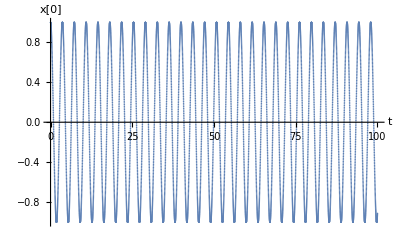

```mathematica
fig = ListPlot[posicao, PlotRange->All, AxesLabel->{"t", "x[0]"}]
```

```mathematica
Export["/home/mariana/Documentos/Ano_2/FC/Lab/Git_Projetos/P2/Para enviar/2a/fig",fig,"PDF"]
```

/home/mariana/Documentos/Ano_2/FC/Lab/Git_Projetos/P2/Para enviar/2a/fig

```mathematica
(*Seria razoável obter um gráfico igual ao gráfico obtido no problema anterior mas tal não se verifica. Acreditamos não está a ser aplicado damping ao sistema apesar de este ser aplicado no ficheiro Forcas.cpp*)
```